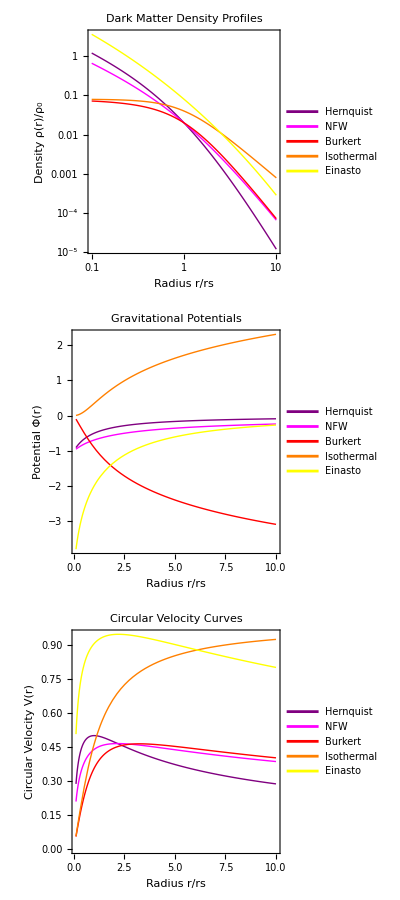

```mathematica
(*Dark Matter Profile Comparison This code compares five common dark matter halo profiles:1. Hernquist (Purple) 2. NFW (Magenta) 3. Burkert (Red) 4. Isothermal (Orange) 5. Einasto (Yellow) We plot three aspects for each profile:-Density profile ρ(r)-Gravitational potential Φ(r)-Circular velocity curve V(r) All plots are shown together for easy comparison with proper legends.*)(*Define the density profiles*)(*Hernquist profile (1990 ApJ 356,359)*)rhoHernquist[r_,a_,M_]:=(M a)/(2 Pi r (r+a)^3)
potentialHernquist[r_,a_,M_]:=-(G M)/(r+a)
vcircHernquist[r_,a_,M_]:=Sqrt[(G M r)/(r+a)^2]

(*NFW profile (Navarro,Frenk& White 1996 ApJ 462,563)*)
rhoNFW[r_,rs_,rho0_]:=rho0/((r/rs) (1+r/rs)^2)
potentialNFW[r_,rs_,rho0_]:=-4 Pi G rho0 rs^3 Log[1+r/rs]/r
vcircNFW[r_,rs_,rho0_]:=Sqrt[4 Pi G rho0 rs^3 (Log[1+r/rs]/r-1/(r+rs))]

(*Burkert profile (1995 ApJ 447,L25)*)
rhoBurkert[r_,rs_,rho0_]:=rho0/((1+r/rs) (1+(r/rs)^2))
potentialBurkert[r_,rs_,rho0_]:=-Pi G rho0 rs^2 (2 ArcTan[r/rs]+Log[(1+r/rs)^2 (1+(r/rs)^2)])
vcircBurkert[r_,rs_,rho0_]:=Sqrt[Pi G rho0 rs^2 (Log[(1+r/rs)^2 (1+(r/rs)^2)]-2 ArcTan[r/rs])/r]

(*Isothermal sphere profile*)
rhoIsothermal[r_,rc_,rho0_]:=rho0/(1+(r/rc)^2)
potentialIsothermal[r_,rc_,rho0_]:=2 Pi G rho0 rc^2 Log[1+(r/rc)^2]
vcircIsothermal[r_,rc_,rho0_]:=Sqrt[4 Pi G rho0 rc^2 (1-(rc/r) ArcTan[r/rc])]

(*Einasto profile (1965 Trudy Astrofizicheskogo Instituta Alma-Ata 5,87)*)
rhoEinasto[r_,rs_,rho0_,alpha_]:=rho0 Exp[-2/alpha ((r/rs)^alpha-1)]
(*Note:Einasto potential and velocity curves require numerical integration*)
potentialEinasto[r_,rs_,rho0_,alpha_]:=-4 Pi G NIntegrate[rhoEinasto[x,rs,rho0,alpha] x^2/x,{x,r,100 rs}]
vcircEinasto[r_,rs_,rho0_,alpha_]:=Sqrt[4 Pi G NIntegrate[rhoEinasto[x,rs,rho0,alpha] x^2,{x,0,r}]/r]

(*Set common parameters for comparison*)
G=1; (*Gravitational constant in appropriate units*)
M=1; (*Characteristic mass*)
a=1;rs=1;rc=1; (*Scale radii-set equal for comparison*)
rho0=1/(4 Pi); (*Characteristic density for normalization*)
alphaEinasto=0.17; (*Typical value for dark matter halos*)

(*Define ranges*)
rmin=0.1;
rmax=10;

(*Create plots*)

(*Density profile comparison*)
densityPlot=LogLogPlot[{rhoHernquist[r,a,M],rhoNFW[r,rs,rho0],rhoBurkert[r,rs,rho0],rhoIsothermal[r,rc,rho0],rhoEinasto[r,rs,rho0,alphaEinasto]},{r,rmin,rmax},PlotStyle->{{Purple,Thick},(*Hernquist*){Magenta,Thick},(*NFW*){Red,Thick},(*Burkert*){Orange,Thick},(*Isothermal*){Yellow,Thick}},(*Einasto*)Frame->True,FrameLabel->{"Radius r/rs","Density ρ(r)/ρ₀"},PlotLegends->Placed[{Style["Hernquist",Purple],Style["NFW",Magenta],Style["Burkert",Red],Style["Isothermal",Orange],Style["Einasto",Yellow]},{Right,Top}],PlotLabel->"Dark Matter Density Profiles",ImageSize->Large];

(*Potential comparison*)
potentialPlot=Plot[{potentialHernquist[r,a,M],potentialNFW[r,rs,rho0],potentialBurkert[r,rs,rho0],potentialIsothermal[r,rc,rho0],Quiet@potentialEinasto[r,rs,rho0,alphaEinasto]},{r,rmin,rmax},PlotStyle->{{Purple,Thick},(*Hernquist*){Magenta,Thick},(*NFW*){Red,Thick},(*Burkert*){Orange,Thick},(*Isothermal*){Yellow,Thick}},(*Einasto*)Frame->True,FrameLabel->{"Radius r/rs","Potential Φ(r)"},PlotLegends->Placed[{Style["Hernquist",Purple],Style["NFW",Magenta],Style["Burkert",Red],Style["Isothermal",Orange],Style["Einasto",Yellow]},{Right,Top}],PlotLabel->"Gravitational Potentials",ImageSize->Large];

(*Velocity curve comparison*)
velocityPlot=Plot[{vcircHernquist[r,a,M],vcircNFW[r,rs,rho0],vcircBurkert[r,rs,rho0],vcircIsothermal[r,rc,rho0],Quiet@vcircEinasto[r,rs,rho0,alphaEinasto]},{r,rmin,rmax},PlotStyle->{{Purple,Thick},(*Hernquist*){Magenta,Thick},(*NFW*){Red,Thick},(*Burkert*){Orange,Thick},(*Isothermal*){Yellow,Thick}},(*Einasto*)Frame->True,FrameLabel->{"Radius r/rs","Circular Velocity V(r)"},PlotLegends->Placed[{Style["Hernquist",Purple],Style["NFW",Magenta],Style["Burkert",Red],Style["Isothermal",Orange],Style["Einasto",Yellow]},{Right,Top}],PlotLabel->"Circular Velocity Curves",ImageSize->Large];

(*Display all plots together*)
Grid[{{densityPlot},{potentialPlot},{velocityPlot}},Spacings->{1,1}]
```